```mathematica
(* parameters
```

```mathematica
f[x_,xi_,h_]:=Exp[-(x-xi)^2/(2h^2)]/Sqrt[2π h]
```

```mathematica
ptmp=Total[Table[f[x,RandomReal[{0,5}],RandomReal[{0.025,0.1}]],{i,1,60}]]
```

1.3862 ⅇ^(-72.8848 (-4.9876+x)^2)+1.85183 ⅇ^(-232.131 (-4.97598+x)^2)+2.18623 ⅇ^(-450.932 (-4.69076+x)^2)+1.35108 ⅇ^(-65.7734 (-4.61986+x)^2)+1.38074 ⅇ^(-71.743 (-4.55214+x)^2)+1.40118 ⅇ^(-76.0855 (-4.4839+x)^2)+2.17601 ⅇ^(-442.561 (-4.4289+x)^2)+1.27794 ⅇ^(-52.6461 (-4.39077+x)^2)+1.38124 ⅇ^(-71.847 (-4.29924+x)^2)+1.36001 ⅇ^(-67.5308 (-4.29196+x)^2)+1.42573 ⅇ^(-81.5596 (-4.24769+x)^2)+1.94984 ⅇ^(-285.316 (-4.14058+x)^2)+1.72605 ⅇ^(-175.205 (-3.89621+x)^2)+2.12533 ⅇ^(-402.751 (-3.86716+x)^2)+2.02698 ⅇ^(-333.22 (-3.82968+x)^2)+1.89815 ⅇ^(-256.242 (-3.82102+x)^2)+1.94099 ⅇ^(-280.169 (-3.80205+x)^2)+1.51269 ⅇ^(-103.354 (-3.77192+x)^2)+1.63232 ⅇ^(-140.137 (-3.60397+x)^2)+1.74433 ⅇ^(-182.744 (-3.4204+x)^2)+1.35772 ⅇ^(-67.076 (-3.39501+x)^2)+1.38131 ⅇ^(-71.8609 (-3.33087+x)^2)+1.26494 ⅇ^(-50.5377 (-3.15507+x)^2)+1.34171 ⅇ^(-63.9678 (-3.15222+x)^2)+1.60663 ⅇ^(-131.521 (-3.14465+x)^2)+1.37542 ⅇ^(-70.6435 (-3.13327+x)^2)+1.72858 ⅇ^(-176.232 (-2.96894+x)^2)+1.83486 ⅇ^(-223.739 (-2.96626+x)^2)+1.42454 ⅇ^(-81.2879 (-2.95513+x)^2)+1.72379 ⅇ^(-174.286 (-2.84014+x)^2)+1.96338 ⅇ^(-293.323 (-2.74219+x)^2)+2.50566 ⅇ^(-778.071 (-2.70072+x)^2)+2.4983 ⅇ^(-768.964 (-2.67883+x)^2)+1.3218 ⅇ^(-60.2553 (-2.64097+x)^2)+1.62754 ⅇ^(-138.501 (-2.53419+x)^2)+2.52212 ⅇ^(-798.714 (-2.43081+x)^2)+1.7818 ⅇ^(-198.958 (-2.14332+x)^2)+2.37519 ⅇ^(-628.232 (-1.95134+x)^2)+1.76624 ⅇ^(-192.102 (-1.95037+x)^2)+1.93475 ⅇ^(-276.584 (-1.76518+x)^2)+2.4393 ⅇ^(-698.856 (-1.69558+x)^2)+1.27911 ⅇ^(-52.8403 (-1.41896+x)^2)+1.33603 ⅇ^(-62.892 (-1.29281+x)^2)+1.42918 ⅇ^(-82.3526 (-1.2147+x)^2)+1.50538 ⅇ^(-101.372 (-1.05471+x)^2)+2.15623 ⅇ^(-426.688 (-0.999961+x)^2)+2.41389 ⅇ^(-670.195 (-0.898637+x)^2)+2.18812 ⅇ^(-452.495 (-0.822863+x)^2)+1.62677 ⅇ^(-138.24 (-0.814003+x)^2)+2.26126 ⅇ^(-516.1 (-0.714309+x)^2)+1.46898 ⅇ^(-91.9172 (-0.708566+x)^2)+1.55806 ⅇ^(-116.322 (-0.582491+x)^2)+1.63569 ⅇ^(-141.298 (-0.576882+x)^2)+1.81138 ⅇ^(-212.503 (-0.535852+x)^2)+1.30849 ⅇ^(-57.864 (-0.419836+x)^2)+1.87365 ⅇ^(-243.268 (-0.395876+x)^2)+1.39055 ⅇ^(-73.8024 (-0.394493+x)^2)+1.73856 ⅇ^(-180.339 (-0.332195+x)^2)+2.00697 ⅇ^(-320.251 (-0.198832+x)^2)+1.41922 ⅇ^(-80.0819 (-0.0106107+x)^2)

```mathematica
p[a_]:=ptmp/.{x->a}
```

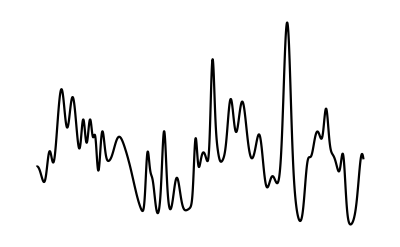

```mathematica
test=Plot[p[a]+0.5Cos[a*5.]-0.05*a^2,{a,0,5},Axes->False,PlotStyle->Black]
```

```mathematica
Export["rugged.pdf",test]
```

rugged.pdf

```mathematica
psmooth=Total[Table[f[x,RandomReal[{0,5}],RandomReal[{0.25,0.3}]],{i,1,20}]];
```

```mathematica
ps[a_]:=psmooth/.{x->a}
```

```mathematica
barrier[a_]:=If[a<0.75,Abs[10*(a-0.75)]^4,
If[a>4.25,Abs[(a-4.25)*10]^4,0.]
]
```

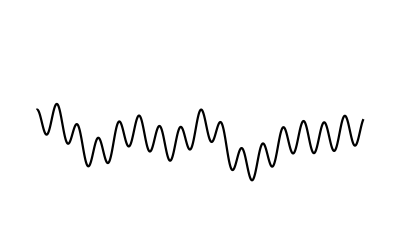

```mathematica
test=Plot[ps[a]+1.0Cos[a*20.]+0.25*(a-2.5)^2,{a,0,5},Axes->False,PlotStyle->Black,PlotRange->{{0.,5.},{-3,10}}]
```

-Graphics3D-

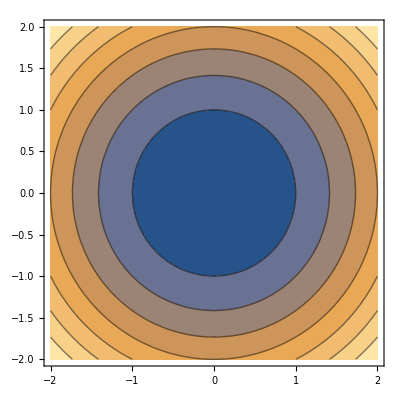

```mathematica
f3d[x_,y_]:=x^2+y^2

a=Plot3D[f3d[x,y],{x,-2,2},{y,-2,2}]
b=ContourPlot[f3d[x,y],{x,-2,2},{y,-2,2}]
```

```mathematica
gr=Graphics3D[{Texture[contourPotentialPlot1],EdgeForm[],Polygon[{{-400,-300,level},{400,-300,level},{400,300,level},{-400,300,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Graphics3D[{a,b}]
```

-Graphics3D-

```mathematica
f
```

```mathematica
contourPotentialPlot1=ContourPlot[f3d[x,y]+x^2+y^2,{x,-2,2},{y,-2,2},PlotRange->{-11,2},Contours->15,Axes->False,PlotPoints->30,PlotRangePadding->0,Frame->False,ColorFunction->"DarkRainbow"];

potential1=Plot3D[f3d[x,y]+x^2+y^2,{x,-2,2},{y,-2,2},Mesh->250,MeshStyle->Opacity[.5],PlotRange->All,ClippingStyle->None,ColorFunction->"Rainbow"
];(*,PlotRange->{-2,2},ClippingStyle->None,MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange}},Lighting->"Neutral"];*)

level=-13;gr=Graphics3D[{Texture[contourPotentialPlot1],EdgeForm[],Polygon[{{-2,-2,level},{2,-2,level},{2,2,level},{-2,2,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"];
```

```mathematica
Show[potential1,gr,PlotRange->All,BoxRatios->{1,1,.6},FaceGrids->{Back,Left},Ticks->False]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"BlueGreenYellow"]
```

```mathematica
(0+1+2+3+4)/5
```

2

```mathematica
Export["smooth.pdf",test]
```

smooth.pdf

```mathematica
g[x1_,x2_,μ_,h_]:=Exp[-Norm[({x1,x2}-μ)]^2/(2h^2)]/(2π*h)
```

```mathematica
cl1=Total[Table[g[x1,x2,{RandomReal[{-1.,-0.15}],RandomReal[{-1,-0.15}]},0.1],{i,40}]];
cl2=Total[Table[g[x1,x2,{RandomReal[{1,0.15}],RandomReal[{1,0.15}]},0.1],{i,40}]];
cl3=Total[Table[g[x1,x2,{RandomReal[{-2,2}],RandomReal[{-2,2}]},0.3],{i,20}]];
```

```mathematica
f3d[x1p_,x2p_]:=-(cl1/.{x1->x1p,x2->x2p})-(cl2/.{x1->x1p,x2->x2p})-4*(cl3/.{x1->x1p,x2->x2p})
```

```mathematica
Plot3D[f3d[x,y],{x,-2,2},{y,-2,2},PlotRange->All]
```

-Graphics3D-

```mathematica
s1=2b1-1
s2=2b2-1
s3=2b3-1
```

-1+2 b1

-1+2 b2

-1+2 b3

```mathematica
s1*s2*s3//Expand
```

-1+2 b1+2 b2-4 b1 b2+2 b3-4 b1 b3-4 b2 b3+8 b1 b2 b3